```mathematica
Needs["FindBounce`"]
```

Single Scalar Field (if function is given)

```mathematica
potential[x_]:=0.5 x^2-0.5 x^3+0.1 x^4;
```

```mathematica
extrema=Block[{x},x/. NSolve[D[potential[x],x]==0,x]]
```

{0.,0.867218,2.88278}

{{0.,0.},{0.867218,0.106491},{2.88278,-0.917038}}

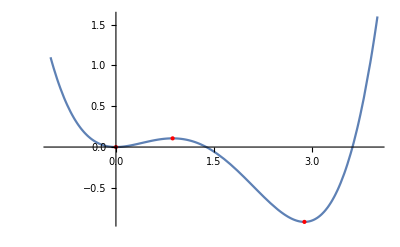

```mathematica
pts=Transpose[{extrema,potential/@extrema}]
Plot[potential[x],{x,-1,4},Epilog->{Red,PointSize[Large],Point[pts]}]
```

```mathematica
bf=FindBounce[potential[x],{x},{extrema[[1]],extrema[[3]]}]
```

BounceFunction[<|Action -> 1515.14, <<7>>, CoefficientsExtension -> {{{0.0514105}, {0.326393}, {1.34994}, {2.32952}, {2.76504}, {2.49936}, {1.64227}, {0.484372}, {-0.581359}, {-1.12759}, {-0.75038}, {0.882558}, {3.99256}, {8.65924}, {14.7982}, {22.1475}, {30.2626}, <<5>>, {51.0844}, {41.2227}, {25.7259}, {4.91427}, {-19.7402}, {-44.7377}, {-62.5527}, {-54.9304}}, <<3>>}|>]

```mathematica
bf["Action"]
```

1515.14

```mathematica
bf["Dimension"]
```

4

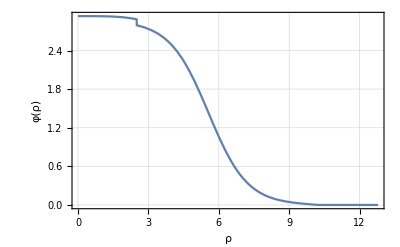

```mathematica
BouncePlot[bf]
```